```mathematica
ClearAll["Global`*"]
(*~ MacOS ~*)
main="/Users/mikhailgaerlan/Box Sync/Education/MSU/2015-2016 Fall/PH 4433 Computational Physics/Homework/Homework 3/ohg6-hw3/";
SetDirectory[main];
$Line=0;
```

# 1

```mathematica
rawdata=Import["1/hw3-1.txt","Data"];
```

```mathematica
data=rawdata[[All,{2,1,3}]];
```

```mathematica
ListPlot3D[data]
```

-Graphics3D-

```mathematica
ListDensityPlot[data,ColorFunction->"GrayTones",InterpolationOrder->0,PlotLabel->"Intensity", BaseStyle->{FontFamily->Times, FontSize->12},Frame->True,FrameLabel->{"z","x"}]
```

-Graphics-

```mathematica
Export["1/intensity.png",%]
```

1/intensity.png

```mathematica
data[[-5;;]]
```

{{3.,4.9375,0.958838},{3.,4.95313,0.975994},{3.,4.96875,0.993807},{3.,4.98438,1.01181},{3.,5.,1.02952}}

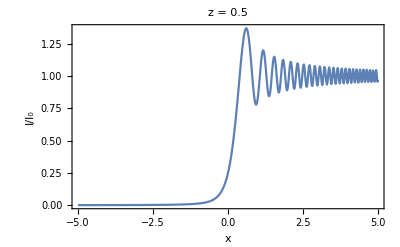
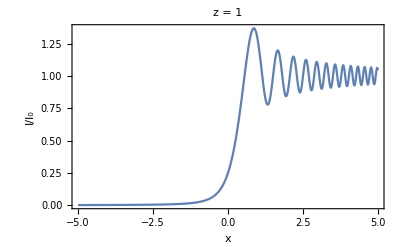
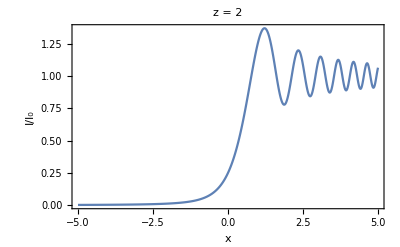
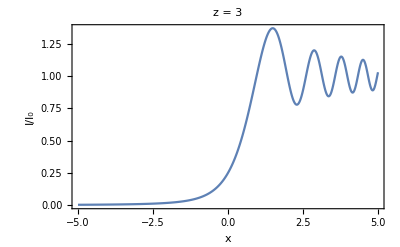

```mathematica
zs=Table[ListLinePlot[Cases[data,{x_,_,_}/;x==z][[All,{2,3}]],FrameLabel->{"x","I/I_0"},PlotLabel->"z = "<>ToString[z],Frame->True,Axes->False,BaseStyle->{FontSize->12,FontFamily->Times}],{z,{0.5,1,2,3}}]
```

```mathematica
Table[Export["1/hw3-1-"<>ToString[i]<>".png",zs[[i]]],{i,1,4}]
```

{1/hw3-1-1.png,1/hw3-1-2.png,1/hw3-1-3.png,1/hw3-1-4.png}

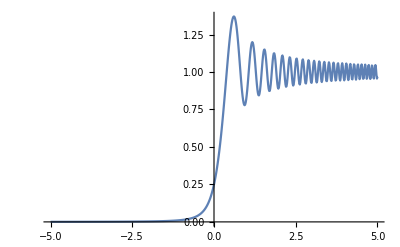

```mathematica
testdata=Import["1/hw3-1-1.txt","Data"];
ListLinePlot[testdata[[All,{1,3}]]]
```

# 2

## sin(x)

```mathematica
rawdata=Import["2/hw3-2-sin.txt","Data"];
rawdata[[;;10]]//TableForm
```

0.1 | 10. | 0.0424646 | -0.0541303 | -0.0873135 | 0.957322 | 1.0544 | 1.08775
0.1 | 3.16228 | 0.00649313 | -0.00650803 | -0.0108463 | 0.993474 | 1.00654 | 1.0109
0.1 | 1. | 0.381688 | 0.837267 | 0.965564 | 0.616396 | 0.158529 | 0.0295883
0.1 | 0.316228 | 0.899453 | 0.978503 | 0.994676 | 0.096031 | 0.0165835 | 0.000329388
0.1 | 0.1 | 0.978434 | 0.993347 | 0.995001 | 0.0166534 | 0.00166583 | 3.32937×10^-6
0.1 | 0.0316228 | 0.991185 | 0.994838 | 0.995004 | 0.00383834 | 0.000166658 | 3.33294×10^-8
0.1 | 0.01 | 0.99394 | 0.994988 | 0.995004 | 0.00106998 | 0.0000166666 | 3.33328×10^-10
0.1 | 0.00316228 | 0.994682 | 0.995003 | 0.995004 | 0.000323952 | 1.66667×10^-6 | 3.33255×10^-12
0.1 | 0.001 | 0.994904 | 0.995004 | 0.995004 | 0.000101001 | 1.66667×10^-7 | 2.90107×10^-14
0.1 | 0.000316228 | 0.994973 | 0.995004 | 0.995004 | 0.0000317953 | 1.66667×10^-8 | 8.70322×10^-15

3.16228×10^-9 | 3.16228×10^-6
1.×10^-8 | 0.00001
3.16228×10^-8 | 0.0000316228

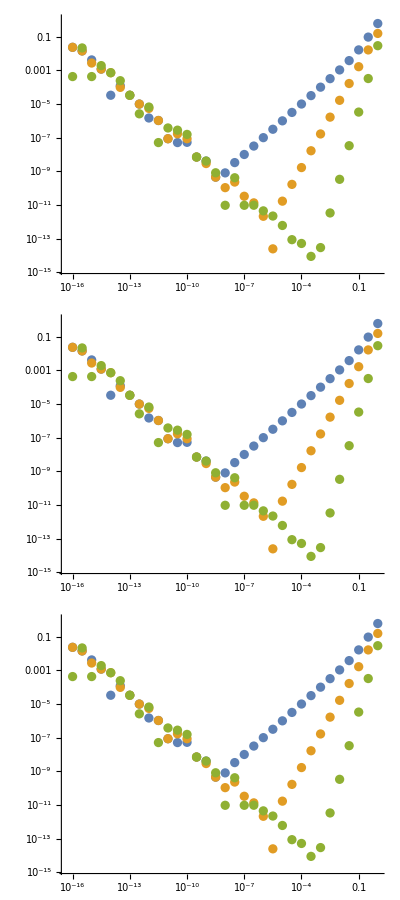

{{FittedModel[-1.47915+1.07105 x],FittedModel[-1.81442+1.9961 x],FittedModel[-3.4777+3.97828 x]},{FittedModel[-0.243868+1.01692 x],FittedModel[-1.8144+1.99611 x],FittedModel[-3.47771+3.97827 x]},{FittedModel[-1.05871+0.950778 x],FittedModel[-1.81429+1.99616 x],FittedModel[-3.47726+3.97866 x]}}

```mathematica
F[x_]:=Sin[x];
xs={0.1,10,100};
datasorted=Table[Table[Cases[rawdata,x_/;Part[x,1]==k][[3;;,{2,j}]],{j,6,8}],{k,{0.1,10,100}}];
Table[(Pick[#1,#2,Min[#2]]&@@Transpose[Cases[datasorted[[i,j]],x_/;Part[x,2]≠0]]*1)[[1]],{i,1,3},{j,1,2}]//TableForm
Table[ListLogLogPlot[datasorted[[1]]],{j,1,3}]//TableForm
model={{LinearModelFit[Log[datasorted[[1,1,;;15]]],x,x],LinearModelFit[Log[datasorted[[1,2,;;8]]],x,x],LinearModelFit[Log[datasorted[[1,3,;;5]]],x,x]},{LinearModelFit[Log[datasorted[[2,1,;;15]]],x,x],LinearModelFit[Log[datasorted[[2,2,;;8]]],x,x],LinearModelFit[Log[datasorted[[2,3,;;5]]],x,x]},{LinearModelFit[Log[datasorted[[3,1,;;15]]],x,x],LinearModelFit[Log[datasorted[[3,2,;;8]]],x,x],LinearModelFit[Log[datasorted[[3,3,;;5]]],x,x]}}
```

```mathematica
Flatten[Table[Exp[model[[i,j]][Log[x]]],{i,1,3},{j,1,3}]]//TableForm//TeXForm
```

\begin{array}{c}
 0.227831 x^{1.07105} \\
 0.162933 x^{1.9961} \\
 0.0308783 x^{3.97828} \\
 0.783591 x^{1.01692} \\
 0.162935 x^{1.99611} \\
 0.0308779 x^{3.97827} \\
 0.346903 x^{0.950778} \\
 0.162954 x^{1.99616} \\
 0.030892 x^{3.97866} \\
\end{array}

```mathematica
Table[{Exp[model[[i,j]]["BestFitParameters"][[1]]],
√(Exp[model[[i,j]]["BestFitParameters"][[1]]]^2*(model[[i,j]]["ParameterErrors"][[1]])^2)}//Column,{i,1,3},{j,1,3}]
```

{{0.227831
0.0442294,0.162933
0.0015473,0.0308783
0.000935037},{0.783591
0.0366855,0.162935
0.00154836,0.0308779
0.00093476},{0.346903
0.0563786,0.162954
0.00155579,0.030892
0.000946277}}

```mathematica
Table[{model[[i,j]]["BestFitParameters"][[2]],
model[[i,j]]["ParameterErrors"][[2]]}//Column,{i,1,3},{j,1,3}]
```

{{1.07105
0.0204986,1.9961
0.0019718,3.97828
0.0107378},{1.01692
0.00494348,1.99611
0.00197311,3.97827
0.0107347},{0.950778
0.0171606,1.99616
0.00198236,3.97866
0.010862}}

```mathematica
plots=Table[Show[ListLogLogPlot[datasorted[[j]],PlotLegends->{"2-point","3-point","5-point"},PlotLabel->"x = "<>ToString[xs[[j]]],LabelStyle->{FontFamily->Times,FontSize->12},Axes->False,Frame->True,FrameTicks->{{Automatic,None},{Automatic,None}},FrameLabel->{"h","ϵ"},GridLines->{{(Abs[(2*$MachineEpsilon)/F''[xs[[j]]]])^(1/2),(Abs[(3*$MachineEpsilon)/F'''[xs[[j]]]])^(1/3)},None}],LogLogPlot[Evaluate[Table[Exp[model[[j,i]][Log[x]]],{i,1,3}]],{x,10,10^-20}]],{j,1,3}];
```

```mathematica
Export["2/plot01sin.png",plots[[1]]];
Export["2/plot10sin.png",plots[[2]]];
Export["2/plot100sin.png",plots[[3]]];
```

```mathematica
Table[{(Abs[(2*$MachineEpsilon)/F''[xs[[j]]]])^(1/2),(Abs[(3*$MachineEpsilon)/F'''[xs[[j]]]])^(1/3)},{j,1,3}]//TableForm
```

6.66956×10^-8 | 8.74807×10^-6
2.85711×10^-8 | 9.2595×10^-6
2.96144×10^-8 | 9.17553×10^-6

## exp(x)

```mathematica
rawdata=Import["2/hw3-2-e.txt","Data"];
rawdata[[;;10]]//TableForm
```

0.1 | 10. | 2.68095×10^7 | 1217.15 | -4.46663×10^6 | 2.42583×10^7 | 1100.32 | 4.04158×10^6
0.1 | 3.16228 | 97.3509 | 4.12079 | -10.7598 | 87.0868 | 2.72864 | 10.7359
0.1 | 1. | 3.5305 | 1.2988 | 1.06368 | 2.19453 | 0.175201 | 0.0375418
0.1 | 0.316228 | 1.54163 | 1.12368 | 1.1048 | 0.394923 | 0.0167502 | 0.000337325
0.1 | 0.1 | 1.22344 | 1.10701 | 1.10517 | 0.107014 | 0.0016675 | 3.3373×10^-6
0.1 | 0.0316228 | 1.14087 | 1.10536 | 1.10517 | 0.0323001 | 0.000166675 | 3.33373×10^-8
0.1 | 0.01 | 1.1163 | 1.10519 | 1.10517 | 0.010067 | 0.0000166667 | 3.33343×10^-10
0.1 | 0.00316228 | 1.10867 | 1.10517 | 1.10517 | 0.00316895 | 1.66667×10^-6 | 3.32393×10^-12
0.1 | 0.001 | 1.10628 | 1.10517 | 1.10517 | 0.00100067 | 1.66667×10^-7 | 2.27033×10^-14
0.1 | 0.000316228 | 1.10552 | 1.10517 | 1.10517 | 0.000316294 | 1.66665×10^-8 | 3.27289×10^-13

1.×10^-8 | 3.16228×10^-6
1.×10^-8 | 0.00001
3.16228×10^-8 | 0.0000316228

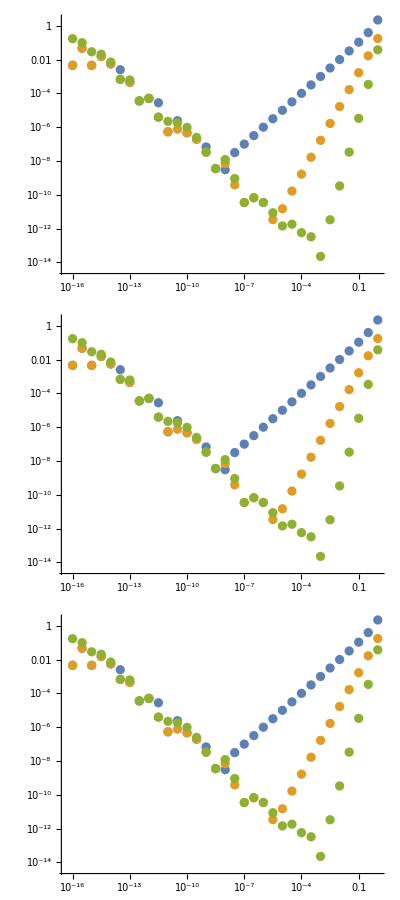

{{FittedModel[0.256499+1.02272 x],FittedModel[-1.76915+2.00389 x],FittedModel[-3.32487+4.02167 x]},{FittedModel[0.253536+1.02213 x],FittedModel[-1.76917+2.00388 x],FittedModel[-3.32487+4.02167 x]},{FittedModel[0.241781+1.01972 x],FittedModel[-1.76928+2.00383 x],FittedModel[-3.32442+4.02206 x]}}

\left(
\begin{array}{ccc}
 1.2924 x^{1.02272} & 0.170478 x^{2.00389} & 0.0359774 x^{4.02167} \\
 1.28857 x^{1.02213} & 0.170475 x^{2.00388} & 0.035977 x^{4.02167} \\
 1.27352 x^{1.01972} & 0.170455 x^{2.00383} & 0.0359935 x^{4.02206} \\
\end{array}
\right)

```mathematica
F[x_]:=Exp[x];
xs={0.1,10,100};
datasorted=Table[Table[Cases[rawdata,x_/;Part[x,1]==k][[3;;,{2,j}]],{j,6,8}],{k,{0.1,10,100}}];
Table[(Pick[#1,#2,Min[#2]]&@@Transpose[Cases[datasorted[[i,j]],x_/;Part[x,2]≠0]]*1)[[1]],{i,1,3},{j,1,2}]//TableForm
Table[ListLogLogPlot[datasorted[[1]]],{j,1,3}]//TableForm
model={{LinearModelFit[Log[datasorted[[1,1,;;15]]],x,x],LinearModelFit[Log[datasorted[[1,2,;;8]]],x,x],LinearModelFit[Log[datasorted[[1,3,;;5]]],x,x]},{LinearModelFit[Log[datasorted[[2,1,;;15]]],x,x],LinearModelFit[Log[datasorted[[2,2,;;8]]],x,x],LinearModelFit[Log[datasorted[[2,3,;;5]]],x,x]},{LinearModelFit[Log[datasorted[[3,1,;;15]]],x,x],LinearModelFit[Log[datasorted[[3,2,;;8]]],x,x],LinearModelFit[Log[datasorted[[3,3,;;5]]],x,x]}}
Table[Exp[model[[i,j]][Log[x]]],{i,1,3},{j,1,3}]//TeXForm
```

```mathematica
Table[{Exp[model[[i,j]]["BestFitParameters"][[1]]],
√(Exp[model[[i,j]]["BestFitParameters"][[1]]]^2*(model[[i,j]]["ParameterErrors"][[1]])^2)}//Column,{i,1,3},{j,1,3}]
```

{{1.2924
0.111426,0.170478
0.00161481,0.0359774
0.00108667},{1.28857
0.111977,0.170475
0.00161596,0.035977
0.00108692},{1.27352
0.114833,0.170455
0.00162347,0.0359935
0.00107475}}

```mathematica
Table[{model[[i,j]]["BestFitParameters"][[2]],
model[[i,j]]["ParameterErrors"][[2]]}//Column,{i,1,3},{j,1,3}]
```

{{1.02272
0.00910372,2.00389
0.00196675,4.02167
0.0107104},{1.02213
0.0091759,2.00388
0.00196818,4.02167
0.010713},{1.01972
0.00952117,2.00383
0.00197756,4.02206
0.0105882}}

```mathematica
plots=Table[Show[ListLogLogPlot[datasorted[[j]],PlotLegends->{"2-point","3-point","5-point"},PlotLabel->"x = "<>ToString[xs[[j]]],LabelStyle->{FontFamily->Times,FontSize->12},Axes->False,Frame->True,FrameTicks->{{Automatic,None},{Automatic,None}},FrameLabel->{"h","ϵ"},GridLines->{{(Abs[(2*$MachineEpsilon)/F''[xs[[j]]]])^(1/2),(Abs[(3*$MachineEpsilon)/F'''[xs[[j]]]])^(1/3)},None}],LogLogPlot[Evaluate[Table[Exp[model[[j,i]][Log[x]]],{i,1,3}]],{x,10,10^-20}]],{j,1,3}];
```

```mathematica
Export["2/plot01e.png",plots[[1]]];
Export["2/plot10e.png",plots[[2]]];
Export["2/plot100e.png",plots[[3]]];
```

```mathematica
Table[{(Abs[(2*$MachineEpsilon)/F''[xs[[j]]]])^(1/2),(Abs[(3*$MachineEpsilon)/F'''[xs[[j]]]])^(1/3)},{j,1,3}]//TableForm
```

2.00457×10^-8 | 8.44716×10^-6
1.41992×10^-10 | 3.11558×10^-7
4.06454×10^-30 | 2.91544×10^-20

# 3

```mathematica
Table[2*NIntegrate[1/(√(1-x^2)√(1-(Sin[theta/2]*x)^2)),{x,-1,1}],{theta,0,π,0.3141593}]
```

{6.28319,6.32216,6.44182,6.65086,6.966,7.4163,8.05307,8.9742,10.3993,13.0212}

```mathematica
rawdata=Import["3/hw3-3.txt","Data"];
rawdata[[;;10]]//TableForm
```

0. | 0 | 2 | 6.28319 | 1.
0.0698132 | 4 | 6 | 6.2851 | 1.0003
0.139626 | 8 | 7 | 6.29085 | 1.00122
0.20944 | 12 | 8 | 6.30045 | 1.00275
0.279253 | 16 | 8 | 6.31395 | 1.0049
0.349066 | 20 | 9 | 6.33137 | 1.00767
0.418879 | 24 | 9 | 6.35279 | 1.01108
0.488692 | 28 | 10 | 6.37827 | 1.01513
0.558505 | 32 | 10 | 6.40791 | 1.01985
0.628319 | 36 | 11 | 6.44182 | 1.02525

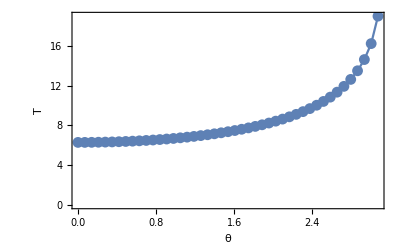

t.png

```mathematica
datat=rawdata[[All,{1,4}]];
Show[ListLinePlot[datat,Frame->True,Axes->False,FrameLabel->{"θ","T"},LabelStyle->{FontFamily->Times,FontSize->12}],ListPlot[datat]]
Export["t.png",%]
```

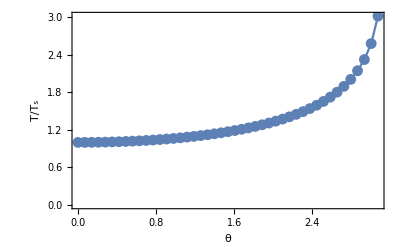

tts.png

```mathematica
datat=rawdata[[All,{1,5}]];
Show[ListLinePlot[datat,Frame->True,Axes->False,FrameLabel->{"θ","T/T_s"},LabelStyle->{FontFamily->Times,FontSize->12}],ListPlot[datat]]
Export["tts.png",%]
```